## Code

### Soundness error formulas

```mathematica
ClearAll@soundnessErrorCommit;
(* Soundness error of the commit phase of FRI, using algebraic batching. 
*)
soundnessErrorCommit[bitsField_, bitsDomain_,bitsRate_,arities_:List, numPolys_,m_]:= Module[
{
rho = 2^(-bitsRate),
domain = 2^bitsDomain,
fieldSize = 2^bitsField
},
	
	Log[2, (numPolys - 1/2)*domain^2*(m+1/2)^7/2 * rho^(-3/2) + (2m+1)*(domain+1)*rho^(-1/2)*Total[2^arities]]
		- bitsField //N
]
```

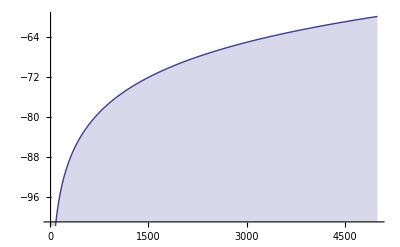

```mathematica
(* the soundness error is increasing in m *)
bitsSec=74;
bitsField = 3*64;
bitsRate=3;
bitsDomain= 15+bitsRate;
arities ={5,4,1};
numPolys=100;
DiscretePlot[
soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys,m],
{m,3,5000}
]
```

```mathematica
ClearAll@soundnessErrorQuery;
(*
Computes the soundness error of the FRI query phase for rate `ρ=2^-bitsRate` and
Johnson proximity parameter `m ≥ 3`.

*)
soundnessErrorQuery[bitsRate_,m_,numSamples_]:= 
	numSamples * (-bitsRate/2 + Log[2, (1+1/(2m))])//N;
```

```mathematica
soundnessErrorQuery[3, 10,90]
```

-128.665

### Number of samples

```mathematica
ClearAll@numSamples;
(* 
Given a security level `bitsSec`, rate `ρ=2^-bitsRate` and Johnson proximity parameter `m ≥ 3,
computes the number of samples so that the query phase soundness error is bounded by `2^-bitsSec`.
*)
Options[numSamples]={
	"Max" -> 10^7
};

numSamples[bitsSec_,bitsRate_,m_, opts:OptionsPattern[]]:= Module[
{
s,
max=OptionValue["Max"]
},
	s=1;
	While[
		soundnessErrorQuery[bitsRate,m,s] > - bitsSec
		&& s ≤ max,
		s++;
	];	
	If[soundnessErrorQuery[bitsRate,m,s] > -bitsSec,
		s= Infinity
	];

s
]
```

```mathematica
bitsSec=112;
bitsRate=3;
m=54;
s=numSamples[bitsSec,bitsRate,m]
soundnessErrorQuery[bitsRate,m,#]&/@{s-1,s}
```

76

{-111.503,-112.989}

### Proximity parameter to Johnson bound

```mathematica
ClearAll@JohnsonProximity;
(*
Johnson bound proximity `m` for the batched FRI.
Given a security level `bitsSec`, the size of the sampling domain `bitsDomain`,
the (logarithmic) code rate `bitsRate`, computes the maximum proximity parameter `m` in 
Lemma 8.2 (adapted to algebraic batching) so that the soundness error in the commitment phase 
of batched FRI is at most `2^-bitsSec`.  
The proximity parameter `m` describes the closeness to the Johnson list decoding bound `1-√ρ` via 
``
	δ = 1 - (1+1/2m)√ρ
``
*)
Options[JohnsonProximity]={
	"Max" -> 10^7
};

JohnsonProximity[
	bitsSec_,bitsField_, bitsDomain_,bitsRate_,arities_:List, numPolys_,  
	opts:OptionsPattern[]
]:= Module[
{
rho = 2^(-bitsRate),
domain = 2^bitsDomain,
fieldSize = 2^bitsField,
maxM= OptionValue["Max"],
m, sol
},
	(* the soundness error for the commitment phase of the batch FRI argument, 
	using algebraic batching
	*)
	m=3;
	sol=3;
	While[ 
		soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys,m] ≤  -bitsSec
		&& m<maxM,
		sol = m;
		m++
	];
	
	If[soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys, sol] > -bitsSec,
		sol = -Infinity
	];

	sol
]
```

```mathematica
bitsSec=67;
bitsField = 2*64;
bitsRate=3;
bitsDomain= 15+bitsRate;
arities ={5,4,1};
numPolys=300;
m=JohnsonProximity[bitsSec,bitsField,bitsDomain,bitsRate,arities,numPolys]
soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys,#]&/@{m,m+1}
s =numSamples[bitsSec,bitsRate,m]
soundnessErrorQuery[bitsRate,m,#]&/@{s-1,s}
```

3

{-67.6221,-65.0841}

53

{-66.4356,-67.7132}

```mathematica
bitsSec=72;
bitsField = 2*64;
bitsRate=4;
bitsDomain= 15+bitsRate;
arities ={5,4,1};
numPolys=300;
m=JohnsonProximity[bitsSec,bitsField,bitsDomain,bitsRate,arities,numPolys]
soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys,#]&/@{m,m+1}
s =numSamples[bitsSec,bitsRate,m]
soundnessErrorQuery[bitsRate,m,#]&/@{s-1,s}
```

3

{-72.3485,-69.8105}

41

{-71.1043,-72.8819}

```mathematica
bitsSec=112;
bitsField = 3*64;
bitsRate=4;
bitsDomain= 15+bitsRate;
arities ={5,4,1};
numPolys=300;
m=JohnsonProximity[bitsSec,bitsField,bitsDomain,bitsRate,arities,numPolys]
soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys,#]&/@{m,m+1}
s =numSamples[bitsSec,bitsRate,m]
soundnessErrorQuery[bitsRate,m,#]&/@{s-1,s}
```

38

{-112.132,-111.874}

57

{-110.944,-112.925}

```mathematica
bitsSec=128;
bitsField = 3*64;
bitsRate=4;
bitsDomain= 15+bitsRate;
arities ={5,4,1};
numPolys=300;
m=JohnsonProximity[bitsSec,bitsField,bitsDomain,bitsRate,arities,numPolys]
soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys,#]&/@{m,m+1}
s =numSamples[bitsSec,bitsRate,m]
soundnessErrorQuery[bitsRate,m,#]&/@{s-1,s}
```

7

{-128.652,-127.388}

68

{-127.331,-129.232}

```mathematica
bitsSec=112;
bitsField = 3*64;
bitsRate=5;
bitsDomain= 15+bitsRate;
arities ={5,4,1};
numPolys=300;
m=JohnsonProximity[bitsSec,bitsField,bitsDomain,bitsRate,arities,numPolys]
soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys,#]&/@{m,m+1}
s =numSamples[bitsSec,bitsRate,m]
soundnessErrorQuery[bitsRate,m,#]&/@{s-1,s}
```

27

{-112.03,-111.67}

46

{-111.309,-113.782}

```mathematica
bitsSec=112; (* if we grind 16 bits *)
bitsField = 3*64;
bitsRate=3;
bitsDomain= 15+bitsRate;
arities ={5,4,1};
numPolys=300;
m=JohnsonProximity[bitsSec,bitsField,bitsDomain,bitsRate,arities,numPolys]
soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,numPolys,#]&/@{m,m+1}
```

54

{-112.123,-111.939}

### Proof size and rough prover cost

```mathematica
ClearAll@prover;
(* Computes the prover cost (as the number of hashes) and the proof size (in field elements)
for a batch FRI prover given a family of groups of polynomials of degree `2^bitsCode` specified by
``
	numPolys ={NumPolys[1], NumPolys[2],..}.
`` 
Each group of `num_polys[i]` polynomials is committed by a single Merkle root.

The FRI parameters are given by 
	- `bitsSec` bits of security, 
	- `bitsRate` for the low degree argument, given in bits (i.e. `2^-rate` is the code rate), 
	- `arities`, the reduction strategy, i.e. the arity list of the FRI reduction steps (i.e. we have 2^arity[i] at step i),
	- `capLevel` gives the level (from the root) of the Merkle caps. (set it to zero for root level)

NOTE: We do not take into account the commitment effort of the initial family of groups 
of polynomials.
*)
Options[prover]={
	"BitsBaseField" -> 64,
	"ExtensionDegree" -> 3 (* the degree of the field extension for FRI*),
	"Hiding" -> False
};

prover[
	numPolys_List, bitsCode_,
	{bitsSec_, bitsRate_, arities_:List, capLevel_},
	opts:OptionsPattern[]
]:= Module[
{
hashSize, (* base FE *)
hashRate, (* base FE *)
hidingRand, (* hiding randomness in base FE *)
bitsDomain, m, s,
proofelems, vals,
proofSize, numHashes,
bitsBaseField = OptionValue["BitsBaseField"],
extDeg = OptionValue["ExtensionDegree"],
bitsField,
hiding = OptionValue["Hiding"]
},
	(* hash parameters, assuming max. 128 bit security *)
	hashSize = Ceiling[256 / bitsBaseField];
	hashRate = hashSize;
	hidingRand = If[hiding, hashSize, 0];

	bitsField = extDeg * bitsBaseField;
	(* the degree of the FRI sampling domain *)
	bitsDomain = bitsCode + bitsRate;

	(* the Johnson proximity *)
	m = JohnsonProximity[bitsSec,bitsField,bitsDomain,bitsRate,arities,Total@numPolys];
	If[m == Infinity,
		Print["Security bound for commit phase not achievable with current extension degree."];
		Return[{Null,Null}]
	];

	(* the query rounds, i.e. the number of samples *)
	s = numSamples[
		bitsSec, bitsRate, m  
	];
	If[s == Infinity, 
		Print["Maximum samples bound reached. Increase it."];
		Return[{Null,Null}]
	];

	proofSize = 0;
	(* The commit phase of FRI: the Merkle caps of the round polynomials trees, 
	plus the revealed polynomial at the end of the FRI reduction.
	 *)
	proofSize += 
(Length[numPolys] + Length[arities]) * 2^capLevel * hashSize + Ceiling[2^bitsCode/2^Total[arities]];

	(* the Merkle paths (without their leaves) per query round.
	These are the paths from
		- the batch polynomial f[0], and the 
		- folded ones f[i], i=1,..Length[arity]-1. 
	*)
	proofelems = (
		bitsDomain - capLevel  (* the batch poly f[0] *)
		+ Total[
			bitsDomain - capLevel - Accumulate@arities[[1;;Length[arities]-1]]
		] (* the folded FRI polys, without the revealed one *)
		) * hashSize;

	(* revealed values per query round:
	The component polynomials are once per round and have values in F, 
	the f[i], i=0,...,d-1 on a coset of size 2^d[i] with d[i]=arity[i] 
	(they have values in the extension field).
	Both might have hiding randomnesses, if required.
	*)
	vals = Total[numPolys] + If[hiding,Length[numPolys]*hidingRand,0];
	(* MT_0..,Length[arity] the coset evaluations of the FRI polynomials *)
	vals += extDeg * Total[2^arities] + If[hiding,Length[arities]*hidingRand,0];
	
	proofSize += s * (proofelems + vals); (* in base FE *)

	(* prover commitment effort, excluding the initial polynomials *)
	numHashes = 2^bitsDomain * (
			(extDeg + hidingRand)* (1 + Total[2^(-Accumulate@arities[[1;;Length[arities]-1]])])
			) / 
			hashRate //Ceiling;


Print@Column[{
	StringForm["Code bits: ``", bitsCode],
	StringForm["Sampling domain bits: ``", bitsDomain],
	StringForm["Number of polynomials for batch open: ``", Total@numPolys],
	StringForm["Johnson proximity m: ``", m],
	StringForm["Soundness error commit phase: 2^``", 
		soundnessErrorCommit[bitsField,bitsDomain,bitsRate,arities,Total@numPolys,m]
	],
	StringForm["Number of query rounds: ``", s],
	StringForm["Soundness error query phase: 2^``", 
		soundnessErrorQuery[bitsRate,m,s]
	],
	StringForm["revealed poly size: `` FE", Ceiling[2^bitsCode/2^Total[arities]]],
	StringForm["per round: `` path elems + `` values = `` FE", proofelems, vals, proofelems + vals],
	StringForm["`` rounds: `` FE", s,  s * (proofelems + vals)]
}];

(* number of compression function invocations, and proof size in Byte*)
{numHashes, proofSize * Ceiling[bitsBaseField/8]}
]
```

## Examples

### 66 bits security

#### degree 2 extensions

```mathematica
bitsSec=66;
bitsCode=12;
bitsRate=3;
arities ={4,3};
numPolys={100,100,100};
capLevel=5; (* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->2,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 15
Number of polynomials for batch open: 300
Johnson proximity m: 6
Soundness error commit phase: 2^-67.3705
Number of query rounds: 48
Soundness error query phase: 2^-66.4571
revealed poly size: 32 FE
per round: 64 path elems + 348 values = 412 FE
48 rounds: 19776 FE

{17408,163584}

```mathematica
bitsSec=66;
bitsCode=12;
bitsRate=4;
arities ={4,3};
numPolys={100,100,100};
capLevel=4;(* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->2,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 16
Number of polynomials for batch open: 300
Johnson proximity m: 4
Soundness error commit phase: 2^-67.5841
Number of query rounds: 37
Soundness error query phase: 2^-67.7128
revealed poly size: 32 FE
per round: 80 path elems + 348 values = 428 FE
37 rounds: 15836 FE

{34816,129504}

```mathematica
bitsSec=66;
bitsCode=12;
bitsRate=5;
arities ={4,3};
numPolys={100,100,100};
capLevel=4; (* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->2,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 17
Number of polynomials for batch open: 300
Johnson proximity m: 3
Soundness error commit phase: 2^-66.6221
Number of query rounds: 29
Soundness error query phase: 2^-66.0506
revealed poly size: 32 FE
per round: 88 path elems + 348 values = 436 FE
29 rounds: 12644 FE

{69632,103968}

#### degree 3 extensions

```mathematica
bitsSec=66;
bitsCode=12;
bitsRate=6;
arities ={4,3};
numPolys={100,100,100};
capLevel=3; (* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 18
Number of polynomials for batch open: 300
Johnson proximity m: 1487
Soundness error commit phase: 2^-66.0029
Number of query rounds: 23
Soundness error query phase: 2^-68.9888
revealed poly size: 32 FE
per round: 104 path elems + 372 values = 476 FE
23 rounds: 10948 FE

{208896,89120}

```mathematica
bitsSec=66;
bitsCode=12;
bitsRate=8;
arities ={4,3};
numPolys={100,100,100};
capLevel=3; (* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 20
Number of polynomials for batch open: 300
Johnson proximity m: 743
Soundness error commit phase: 2^-66.0063
Number of query rounds: 17
Soundness error query phase: 2^-67.9835
revealed poly size: 32 FE
per round: 120 path elems + 372 values = 492 FE
17 rounds: 8364 FE

{835584,68448}

```mathematica
bitsSec=66;
bitsCode=12;
bitsRate=10;
arities ={4,3};
numPolys={100,100,100};
capLevel=3;(* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 22
Number of polynomials for batch open: 300
Johnson proximity m: 371
Soundness error commit phase: 2^-66.0131
Number of query rounds: 14
Soundness error query phase: 2^-69.9728
revealed poly size: 32 FE
per round: 136 path elems + 372 values = 508 FE
14 rounds: 7112 FE

{3342336,58432}

### 112 bits security

#### degree 3 extensions

```mathematica
bitsSec=112;
bitsCode=12;
bitsRate=6;
arities ={4,3};
numPolys={100,100,100};
capLevel=4; (* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 18
Number of polynomials for batch open: 300
Johnson proximity m: 15
Soundness error commit phase: 2^-112.094
Number of query rounds: 38
Soundness error query phase: 2^-112.202
revealed poly size: 32 FE
per round: 96 path elems + 372 values = 468 FE
38 rounds: 17784 FE

{208896,145088}

```mathematica
bitsSec=112;
bitsCode=12;
bitsRate=8;
arities ={4,3};
numPolys={100,100,100};
capLevel=4; (* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 20
Number of polynomials for batch open: 300
Johnson proximity m: 7
Soundness error commit phase: 2^-112.425
Number of query rounds: 29
Soundness error query phase: 2^-113.113
revealed poly size: 32 FE
per round: 112 path elems + 372 values = 484 FE
29 rounds: 14036 FE

{835584,115104}

```mathematica
bitsSec=112;
bitsCode=12;
bitsRate=10;
arities ={4,3};
numPolys={100,100,100};
capLevel=4; (* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 22
Number of polynomials for batch open: 300
Johnson proximity m: 3
Soundness error commit phase: 2^-113.122
Number of query rounds: 24
Soundness error query phase: 2^-114.663
revealed poly size: 32 FE
per round: 128 path elems + 372 values = 500 FE
24 rounds: 12000 FE

{3342336,98816}

### 108 bits security

#### degree 3 extensions

```mathematica
bitsSec=109;
bitsCode=12;
bitsRate=11;
arities ={4,3};
numPolys={100,100,100};
capLevel=4;(* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 23
Number of polynomials for batch open: 300
Johnson proximity m: 3
Soundness error commit phase: 2^-109.622
Number of query rounds: 21
Soundness error query phase: 2^-110.83
revealed poly size: 32 FE
per round: 136 path elems + 372 values = 508 FE
21 rounds: 10668 FE

{6684672,88160}

### 128 bits security

#### degree 3 extensions

```mathematica
bitsSec=128;
bitsCode=12;
bitsRate=3;
arities ={4,3};
numPolys={100,100,100};
capLevel=6;(* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 15
Number of polynomials for batch open: 300
Johnson proximity m: 8
Soundness error commit phase: 2^-128.661
Number of query rounds: 91
Soundness error query phase: 2^-128.541
revealed poly size: 32 FE
per round: 56 path elems + 372 values = 428 FE
91 rounds: 38948 FE

{26112,322080}

```mathematica
bitsSec=128;
bitsCode=12;
bitsRate=4;
arities ={4,3};
numPolys={100,100,100};
capLevel=5;(* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 16
Number of polynomials for batch open: 300
Johnson proximity m: 5
Soundness error commit phase: 2^-129.558
Number of query rounds: 69
Soundness error query phase: 2^-128.512
revealed poly size: 32 FE
per round: 72 path elems + 372 values = 444 FE
69 rounds: 30636 FE

{52224,250464}

```mathematica
bitsSec=128;
bitsCode=12;
bitsRate=5;
arities ={4,3};
numPolys={100,100,100};
capLevel=5;(* set to minimize the proof size *)
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 17
Number of polynomials for batch open: 300
Johnson proximity m: 4
Soundness error commit phase: 2^-128.084
Number of query rounds: 55
Soundness error query phase: 2^-128.154
revealed poly size: 32 FE
per round: 80 path elems + 372 values = 452 FE
55 rounds: 24860 FE

{104448,204256}

```mathematica
bitsSec=128;
bitsCode=12;
bitsRate=6;
arities ={4,3};
numPolys={100,100,100};
capLevel=5;
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 12
Sampling domain bits: 18
Number of polynomials for batch open: 300
Johnson proximity m: -∞
Soundness error commit phase: 2^∞
Number of query rounds: 43
Soundness error query phase: 2^-129.
revealed poly size: 32 FE
per round: 88 path elems + 372 values = 460 FE
43 rounds: 19780 FE

{208896,163616}

## (similar to) ethSTARK parameters

#### 80 bit security

```mathematica
bitsSec=80;
bitsCode=20;
bitsRate=2;
arities ={4,3};
numPolys={100,100};
capLevel=4;
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 20
Sampling domain bits: 22
Number of polynomials for batch open: 200
Johnson proximity m: 322
Soundness error commit phase: 2^-80.0277
Number of query rounds: 81
Soundness error query phase: 2^-80.8187
revealed poly size: 8192 FE
per round: 128 path elems + 272 values = 400 FE
81 rounds: 32400 FE

{3342336,326784}

#### 100 bit security

```mathematica
bitsSec=100;
bitsCode=20;
bitsRate=2;
arities ={4,3};
numPolys={100,100};
capLevel=4;
{numHashes, proofBytes}=prover[numPolys, bitsCode, {bitsSec,bitsRate,arities,capLevel},
"BitsBaseField"->64,
"ExtensionDegree"->3,
"Hiding"->False
]
```

Code bits: 20
Sampling domain bits: 22
Number of polynomials for batch open: 200
Johnson proximity m: 44
Soundness error commit phase: 2^-100.03
Number of query rounds: 102
Soundness error query phase: 2^-100.337
revealed poly size: 8192 FE
per round: 128 path elems + 272 values = 400 FE
102 rounds: 40800 FE

{3342336,393984}